```mathematica
f[x_]:=(√(9 x^6-x))/(x^3+x)
```

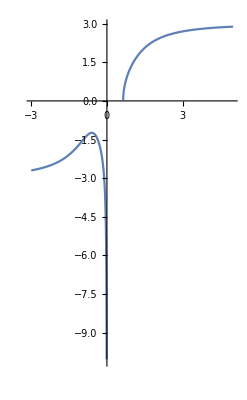

```mathematica
Plot[f[x],{x,-3,5},Exclusions->True,AspectRatio->Automatic]
```

```mathematica
StringForm["Left Hand Limit : ``",Limit[f[x],x->∞,Direction->1]]
StringForm["Right Hand Limit: ``",Limit[f[x],x->∞,Direction->-1]]
```

Left Hand Limit : 3

Right Hand Limit: 3